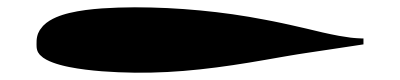

```mathematica
coordsNACA={{1.,0.},{0.995,-0.00029},{0.99,-0.00059},{0.98,-0.00117},{0.97,-0.00176},{0.96,-0.00234},{0.95,-0.00292},{0.925,-0.00438},{0.9,-0.00584},{0.875,-0.00729},{0.85,-0.00874},{0.825,-0.01018},{0.8,-0.01167},{0.775,-0.01327},{0.75,-0.01492},{0.725,-0.01661},{0.7,-0.0183},{0.65,-0.02157},{0.6,-0.02459},{0.55,-0.02728},{0.5,-0.02957},{0.45,-0.0314},{0.4,-0.03269},{0.35,-0.0334},{0.3,-0.0335},{0.25,-0.03297},{0.2,-0.03183},{0.175,-0.03097},{0.15,-0.02989},{0.125,-0.02852},{0.1,-0.0268},{0.09,-0.02598},{0.08,-0.02506},{0.07,-0.02403},{0.06,-0.02286},{0.05,-0.02152},{0.04,-0.01996},{0.03,-0.01808},{0.02,-0.01569},{0.01,-0.01228},{0.005,-0.00959},{0.004,-0.00885},{0.003,-0.00796},{0.002,-0.00686},{0.001,-0.00531},{0.0008,-0.00489},{0.0006,-0.0044},{0.0004,-0.00379},{0.0002,-0.00277},{0.,0.},{0.,0.},{0.0002,0.00445},{0.0004,0.00549},{0.0006,0.00626},{0.0008,0.00687},{0.001,0.00741},{0.002,0.00943},{0.003,0.01091},{0.004,0.01212},{0.005,0.01315},{0.01,0.01695},{0.02,0.02192},{0.03,0.02539},{0.04,0.02807},{0.05,0.03024},{0.06,0.03206},{0.07,0.0336},{0.08,0.03493},{0.09,0.03608},{0.1,0.03709},{0.125,0.03911},{0.15,0.04062},{0.175,0.04173},{0.2,0.04255},{0.25,0.04351},{0.3,0.04385},{0.35,0.04362},{0.4,0.04293},{0.45,0.04176},{0.5,0.04015},{0.55,0.0381},{0.6,0.03559},{0.65,0.03258},{0.7,0.02906},{0.725,0.0272},{0.75,0.0252},{0.775,0.0231},{0.8,0.0209},{0.825,0.0187},{0.85,0.0164},{0.875,0.0141},{0.9,0.012},{0.925,0.0101},{0.95,0.0086},{0.96,0.008},{0.97,0.0076},{0.98,0.0073},{0.99,0.0071},{0.995,0.007},{1.,0.007}};
Graphics[{Polygon[coordsNACA],RGBColor[0.57,0.06,0.06],Opacity[0.01]},AspectRatio->Automatic]
```

```mathematica
Graphics[Polygon[coordsNACA],{0,0}]
```

Polygon[…]

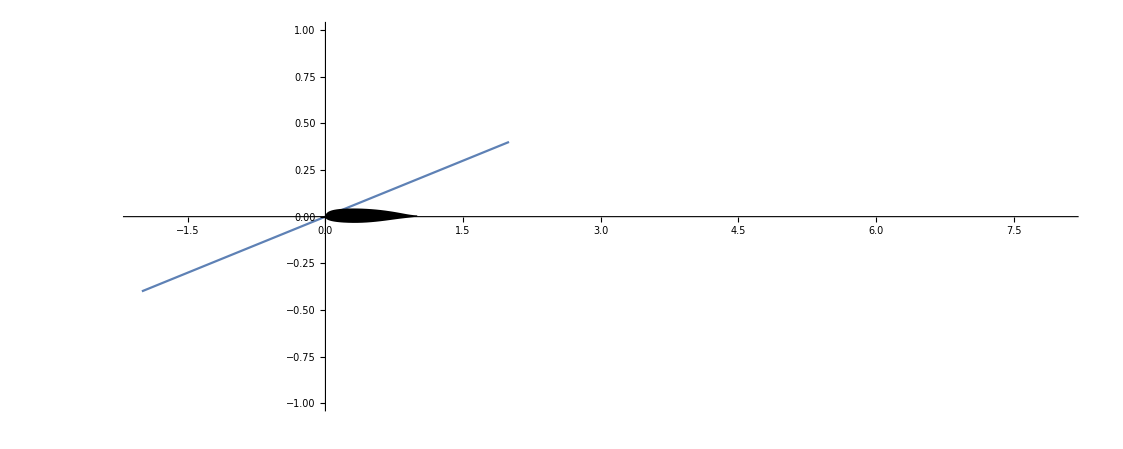

```mathematica
Show[Plot[0.2x,{x,-2,2},PlotRange->{{-2,8},{-1,1}},AspectRatio->Automatic],Graphics[Polygon[coordsNACA]]]
```

```mathematica
?DirichletCondition
```

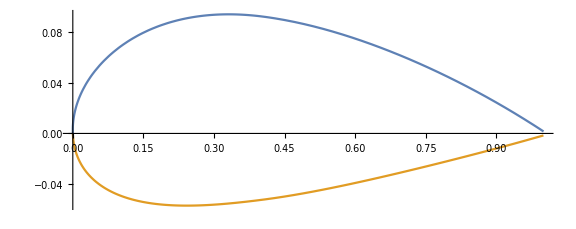

```mathematica
ClearAll[NACA2415];
NACA2415[{m_,p_,t_},x_]:=Module[{},yc=Piecewise[{{m/p^2 (2 p x-x^2),0<=x<p},{m/(1-p)^2 ((1-2 p)+2 p x-x^2),p<=x<=1}}];
yt=5 t (0.2969 Sqrt[x]-0.1260 x-0.3516 x^2+0.2843 x^3-0.1015 x^4);
θ=ArcTan@Piecewise[{{(m*(2*p-2*x))/p^2,0<=x<p},{(m*(2*p-2*x))/(1-p)^2,p<=x<=1}}];
{{x-yt Sin[θ],yc+yt Cos[θ]},{x+yt Sin[θ],yc-yt Cos[θ]}}];

m=0.02;
pp=0.4;
tk=0.15;
pe=NACA2415[{m,pp,tk},x];
ParametricPlot[pe,{x,0,1},ImageSize->Large,Exclusions->None]

ClearAll[myLoop];
myLoop[n1_,n2_]:=Join[Table[{n,n+1},{n,n1,n2-1,1}],{{n2,n1}}]
Needs["NDSolve`FEM`"];(*angle of attack*)alpha=-Pi/32;
rt=RotationTransform[alpha];
a=Table[pe,{x,0,1,0.01}];(*table of coordinates around aerofoil*)p0={pp,tk/2};(*point inside aerofoil*)x1=-1;x2=2;(*domain dimensions*)y1=-1;y2=1;(*domain dimensions*)coords=Join[{{x1,y1},{x2,y1},{x2,y2},{x1,y2}},rt@a[[All,2]],rt@Reverse[a[[All,1]]]];
nn=Length@coords;
bmesh=ToBoundaryMesh["Coordinates"->coords,"BoundaryElements"->{LineElement[myLoop[1,4]],LineElement[myLoop[5,nn]]},"RegionHoles"->{rt@p0}];
mesh=ToElementMesh[bmesh,AccuracyGoal->5,PrecisionGoal->5,"MaxCellMeasure"->0.0005,"MaxBoundaryCellMeasure"->0.01];
ClearAll[x,y,ϕ];
sol=NDSolveValue[{D[ϕ[x,y],x,x]+D[ϕ[x,y],y,y]==NeumannValue[1,x==x1&&y1<=y<=y2]+NeumannValue[-1,x==x2&&y1<=y<=y2],DirichletCondition[ϕ[x,y]==0,x==0&&y==0]},ϕ,{x,y}∈mesh];
ClearAll[vel];
vel=Evaluate[Grad[sol[x,y],{x,y}]];
```

```mathematica
bcs={DirichletCondition[{u[x,y]==1,v[x,y]==0},x==x1],DirichletCondition[{u[x,y]==vel[[1]],v[x,y]==vel[[2]]},y==y1||y==y2],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<=x<=1],DirichletCondition[{p[x,y]==1},x==x2]};

op={Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][u[x,y],{x,y}],{x,y}]+ρ*{{u[x,y],v[x,y]}}.Inactive[Grad][u[x,y],{x,y}]+Derivative[1,0][p][x,y],Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]+ρ*{{u[x,y],v[x,y]}}.Inactive[Grad][v[x,y],{x,y}]+Derivative[0,1][p][x,y],Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]}/. {μ->10^(-3),ρ->1};
pde=op=={0,0,0};{xVel,yVel,pressure}=NDSolveValue[{pde,bcs},{u,v,p},Element[{x,y},mesh],Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}];
```

```mathematica
{Show[ContourPlot[Norm[{xVel[x,y],yVel[x,y]}],Element[{x,y},mesh],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All,AspectRatio->Automatic,Epilog->{Line[coords[[5;;nn]]]},Contours->20],StreamPlot[{xVel[x,y],yVel[x,y]},Element[{x,y},mesh],StreamStyle->LightGray,AspectRatio->Automatic]],ContourPlot[pressure[x,y],Element[{x,y},mesh],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All,AspectRatio->Automatic,Epilog->{Line[coords[[5;;nn]]]},Contours->20]}
```

{-Graphics-,-Graphics-}

```mathematica
ydw=Interpolation[Take[coords[[5;;nn]],101]];yup=Interpolation[Take[coords[[5;;nn]],-101]];
force=With[{umean=1,Y2=ydw'[x],Y1=yup'[x],ρ=1,μ=10^-3,dux=D[xVel[x,y],x],duy=D[xVel[x,y],y],dvx=D[yVel[x,y],x],dvy=D[yVel[x,y],y]},Function[X,Block[{x,y,nx,ny,fx,fy,p},{x,y}=X;
p=pressure[x,y];
nx=If[y>x Tan[alpha],-Y1/Sqrt[1+Y1^2],Y2/Sqrt[1+Y2^2]];
ny=If[y>x Tan[alpha],1/Sqrt[1+Y1^2],-1/Sqrt[1+Y2^2]];
fx=nx*p+μ*(-2*nx*dux-ny*(duy+dvx));
fy=ny*p+μ*(-nx*(dvx+duy)-2*ny*dvy);
{fx,fy}]]];



{fdrag,flift}=NIntegrate[force[{x,y}],{x,y}∈Line[coords[[5;;nn]]],AccuracyGoal->3,PrecisionGoal->3]//AbsoluteTiming
```

{164.67,{-0.0809347,-0.139907}}